```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"bg_data"];
```

```mathematica
<<"../fourdiff.wl"
```

```mathematica
Nt=128;
```

```mathematica
dealias[f_,Nt_]:=Module[{},Re[√Nt InverseFourier[halve[1/(√(2Nt))Fourier[f],Nt]]]]
```

```mathematica
xgrid=Import["loggrid.dat"][[;;,1]];
```

```mathematica
Delta=Import["Delta.dat","List"]//First
```

3.27186

```mathematica
tgrid=Range[0,Delta,Delta/Nt ];
```

### Process data into interpolating functions (not necessary to evaluate every time)

#### Evolution data

```mathematica
f=Import["fB.dat"]//Flatten;
u=Import["uB.dat"]//Flatten;
v=Import["vB.dat"]//Flatten;
ia2=Import["ia2B.dat"]//Flatten;
```

```mathematica
nx=(f//Length)/(2*Nt)
```

8001

```mathematica
fvals=TakeList[f//Flatten,ConstantArray[2*Nt,nx]];
uvals=TakeList[u//Flatten,ConstantArray[2*Nt,nx]];
vvals=TakeList[v//Flatten,ConstantArray[2*Nt,nx]];
ia2vals=TakeList[ia2//Flatten,ConstantArray[2*Nt,nx]];
```

```mathematica
fvals=Table[dealias[fvals[[i]],Nt],{i,1,nx}];
uvals=Table[dealias[uvals[[i]],Nt],{i,1,nx}];
vvals=Table[dealias[vvals[[i]],Nt],{i,1,nx}];
ia2vals=Table[dealias[ia2vals[[i]],Nt],{i,1,nx}];
```

#### Taylor data

```mathematica
nL=500;
nR=500;
```

```mathematica
Rxgrid=Range[0.999,1,(1-0.999)/nR][[2;;]];
Lxgrid=Range[0,0.001,0.001/nL][[;;-2]];
```

```mathematica
fRcoeff=Import["../R_taylor/fright.junk"];
uRcoeff=Import["../R_taylor/uright.junk"];
vRcoeff=Import["../R_taylor/vright.junk"];
ia2Rcoeff=Import["../R_taylor/ia2right.junk"];
```

```mathematica
{f0,f1,f2}=Table[dealias[fRcoeff[[;;,i]],Nt],{i,1,3}];
{u0,u1,u2}=Table[dealias[uRcoeff[[;;,i]],Nt],{i,1,3}];
{v0,v1,v2}=Table[dealias[vRcoeff[[;;,i]],Nt],{i,1,3}];
{ia20,ia21,ia22}=Table[dealias[ia2Rcoeff[[;;,i]],Nt],{i,1,3}];
```

```mathematica
fRvals=Table[f0+(Rxgrid[[i]]-1)*f1+(Rxgrid[[i]]-1)^2*f2,{i,1,nR}];
uRvals=Table[u0+(Rxgrid[[i]]-1)*u1+(Rxgrid[[i]]-1)^2*u2,{i,1,nR}];
vRvals=Table[v0+(Rxgrid[[i]]-1)*v1+(Rxgrid[[i]]-1)^2*v2,{i,1,nR}];
ia2Rvals=Table[ia20+(Rxgrid[[i]]-1)*ia21+(Rxgrid[[i]]-1)^2*ia22,{i,1,nR}];
```

```mathematica
fLcoeff=Import["../L_taylor/fleft.junk"];
uLcoeff=Import["../L_taylor/uleft.junk"];
vLcoeff=Import["../L_taylor/vleft.junk"];
ia2Lcoeff=Import["../L_taylor/ia2left.junk"];
```

```mathematica
{f0,f2,f4}=Table[dealias[fLcoeff[[;;,i]],Nt],{i,1,3}];
{u1,u2,u3,u4,u5}=Table[dealias[uLcoeff[[;;,i]],Nt],{i,1,5}];
{v1,v2,v3,v4,v5}=Table[dealias[vLcoeff[[;;,i]],Nt],{i,1,5}];
{ia22,ia24}=Table[dealias[ia2Lcoeff[[;;,i]],Nt],{i,1,2}];
```

```mathematica
fLvals=Table[f0+(Lxgrid[[i]])^2*f2+(Lxgrid[[i]])^4*f4,{i,1,nL}];
uLvals=Table[u1*Lxgrid[[i]]+(Lxgrid[[i]])^2*u2+(Lxgrid[[i]]^3)*u3+(Lxgrid[[i]]^4)*u4+(Lxgrid[[i]]^5)*u5,{i,1,nL}];
vLvals=Table[v1*Lxgrid[[i]]+(Lxgrid[[i]])^2*v2+(Lxgrid[[i]]^3)*v3+(Lxgrid[[i]]^4)*v4+(Lxgrid[[i]]^5)*v5,{i,1,nL}];
ia2Lvals=Table[1+(Lxgrid[[i]])^2*ia22+(Lxgrid[[i]])^4*ia24,{i,1,nL}];
```

#### Combine

```mathematica
xgridtot=Join[Lxgrid,xgrid,Rxgrid];
```

```mathematica
fvals=Join[fLvals,fvals,fRvals];
uvals=Join[uLvals,uvals,uRvals];
vvals=Join[vLvals,vvals,vRvals];
ia2vals=Join[ia2Lvals,ia2vals,ia2Rvals];
```

```mathematica
(*Extend time interval to include last point (copy of the first)*)
fvalsext=Transpose[Join[Transpose[fvals],{fvals[[;;,1]]}]];
uvalsext=Transpose[Join[Transpose[uvals],{uvals[[;;,1]]}]];
vvalsext=Transpose[Join[Transpose[vvals],{vvals[[;;,1]]}]];
ia2valsext=Transpose[Join[Transpose[ia2vals],{ia2vals[[;;,1]]}]];
```

```mathematica
fvalsext//Dimensions
```

{9001,129}

```mathematica
ftab=Flatten[Table[{tgrid[[i]],xgridtot[[j]],fvalsext[[j,i]]},{i,1,Nt+1},{j,1,nx+nR+nL}],1];
utab=Flatten[Table[{tgrid[[i]],xgridtot[[j]],uvalsext[[j,i]]},{i,1,Nt+1},{j,1,nx+nR+nL}],1];
vtab=Flatten[Table[{tgrid[[i]],xgridtot[[j]],vvalsext[[j,i]]},{i,1,Nt+1},{j,1,nx+nR+nL}],1];
ia2tab=Flatten[Table[{tgrid[[i]],xgridtot[[j]],ia2valsext[[j,i]]},{i,1,Nt+1},{j,1,nx+nR+nL}],1];
```

```mathematica
finterp=Interpolation[ftab];
uinterp=Interpolation[utab];
vinterp=Interpolation[vtab];
ia2interp=Interpolation[ia2tab];
```

```mathematica
Save["finterp.res",finterp]
Save["uinterp.res",uinterp]
Save["vinterp.res",vinterp]
Save["ia2interp.res",ia2interp]
```

### get saved interpolations

```mathematica
finterp=Get["finterp.res"];
Uinterp=Get["uinterp.res"];
Vinterp=Get["vinterp.res"];
ia2interp=Get["ia2interp.res"];
```

```mathematica
GraphicsRow[{Plot3D[finterp[t,x],{t,tgrid[[1]],tgrid[[-1]]},{x,0,1},ImageSize->350,PlotLabel->"f"],Plot3D[Uinterp[t,x],{t,tgrid[[1]],tgrid[[-1]]},{x,0,1},ImageSize->350,PlotLabel->"U"],Plot3D[Vinterp[t,x],{t,tgrid[[1]],tgrid[[-1]]},{x,0,1},ImageSize->350,PlotLabel->"V"],Plot3D[ia2interp[t,x],{t,tgrid[[1]],tgrid[[-1]]},{x,0,1},ImageSize->350,PlotRange->All,PlotLabel->"ia2"]}]
```

-Graphics-

```mathematica
Plot3D[ia2interp[t,x],{t,tgrid[[1]],tgrid[[-1]]},{x,0,0.2},ImageSize->350,PlotRange->All,PlotLabel->"ia2"]
```

-Graphics3D-

### On - shell replacements

```mathematica
repleom={Derivative[0,1][f][t,r]->-((-3+Dim) f[t,r] (-1+ia2[t,r]))/(r ia2[t,r]),Derivative[0,1][ia2][t,r]->(8 (-3+Dim)-ia2[t,r] (8 (-3+Dim)+(-2+Dim)^3 Uu[t,r]^2+(-2+Dim)^3 Vv[t,r]^2))/(8 r),Derivative[1,0][ia2][t,r]->3-Dim+(-3+Dim) ia2[t,r]+((-2+Dim)^3 ia2[t,r] ((r+f[t,r]) Uu[t,r]^2+(r-f[t,r]) Vv[t,r]^2))/(8 r),Derivative[0,1][Uu][t,r]->(f[t,r] ((6-2 Dim+(-2+Dim) ia2[t,r]) Uu[t,r]+(-2+Dim) ia2[t,r] Vv[t,r])-2 r ia2[t,r] Derivative[1,0][Uu][t,r])/(2 r (r+f[t,r]) ia2[t,r]),Derivative[0,1][Vv][t,r]->-(f[t,r] (-2 (-3+Dim) Vv[t,r]+(-2+Dim) ia2[t,r] (Uu[t,r]+Vv[t,r]))+2 r ia2[t,r] Derivative[1,0][Vv][t,r])/(2 r (r-f[t,r]) ia2[t,r])};
```

```mathematica
dtrepleom=D[repleom,t];
```

```mathematica
drrepleom=D[repleom,r];
```

```mathematica
ainvrepl={a[t,r]->1/(√ia2[t,r]),D[a[t,r], t]->D[1/(√ia2[t,r]), t],D[a[t,r], r]->D[1/(√ia2[t,r]), r],D[a[t,r], r,t]->D[1/(√ia2[t,r]), r,t],D[a[t,r], r,r]->D[1/(√ia2[t,r]), r,r],D[a[t,r], t,t]->D[1/(√ia2[t,r]), t,t]};
```

## Euler number

### Curvature definitions

```mathematica
n=4;
Dim=4;
```

```mathematica
xx={t,r,theta,phi};
g={{ⅇ^(-2 t) a[t,r]^2 (r^2-f[t,r]^2) ,-ⅇ^(-2 t) r*a[t,r]^2,0,0},{-ⅇ^(-2 t) r*a[t,r]^2,ⅇ^(-2 t) a[t,r]^2,0,0},{0,0,r^2 ⅇ^(-2t),0},{0,0,0,r^2 ⅇ^(-2t)Sin[theta]^2}};
```

```mathematica
InverseMetric[g_]:=Simplify[Inverse[g]]
ChristoffelSymbol[g_,xx_]:=Block[{n,ig,res},n=Length[g];ig=InverseMetric[g];
res=Table[(1/2)*Sum[ig[[i,s]]*(-D[g[[j,k]],xx[[s]]]+D[g[[j,s]],xx[[k]]]+D[g[[s,k]],xx[[j]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}];
Simplify[res]]
RiemannTensor[g_,xx_]:=Block[{n,Chr,res},n=Length[g];Chr=ChristoffelSymbol[g,xx];
res=Table[D[Chr[[i,k,m]],xx[[l]]]-D[Chr[[i,k,l]],xx[[m]]]+Sum[Chr[[i,s,l]]*Chr[[s,k,m]],{s,1,n}]-Sum[Chr[[i,s,m]]*Chr[[s,k,l]],{s,1,n}],{i,1,n},{k,1,n},{l,1,n},{m,1,n}];
Simplify[res]]
RicciTensor[g_,xx_]:=Block[{Rie,res,n},n=Length[g];Rie=RiemannTensor[g,xx];
res=Table[Sum[Rie[[s,i,s,j]],{s,1,n}],{i,1,n},{j,1,n}];
Simplify[res]]
RicciScalar[g_,xx_]:=Block[{Ricc,ig,res,n},n=Length[g];Ricc=RicciTensor[g,xx];ig=InverseMetric[g];
res=Sum[ig[[s,i]] Ricc[[s,i]],{s,1,n},{i,1,n}];
Simplify[res]]
```

```mathematica
ginv=InverseMetric[g];
```

```mathematica
riem=RiemannTensor[g,xx];
```

```mathematica
riemsqu=Sum[ginv[[l,j]]*ginv[[k,b]]*riem[[i,j,m,b]]*riem[[m,k,i,l]],{i,1,n},{j,1,n},{k,1,n},{m,1,n},{l,1,n},{b,1,n}]//Simplify;
```

```mathematica
riemsqu=riemsqu/.ainvrepl/.drrepleom/.dtrepleom/.repleom//Simplify
```

(4 ⅇ^(4 t) (3-2 ia2[t,r] (3+2 Uu[t,r] Vv[t,r])+ia2[t,r]^2 (3+4 Uu[t,r] Vv[t,r]+8 Uu[t,r]^2 Vv[t,r]^2)))/r^4

```mathematica
ric=RicciTensor[g,xx];
```

```mathematica
ricsqu=Sum[ginv[[i,k]]*ginv[[j,l]]*ric[[i,j]]*ric[[k,l]],{i,1,n},{j,1,n},{k,1,n},{l,1,n}];
```

```mathematica
ricsqu=ricsqu/.ainvrepl/.drrepleom/.dtrepleom/.repleom//Simplify
```

(16 ⅇ^(4 t) ia2[t,r]^2 Uu[t,r]^2 Vv[t,r]^2)/r^4

```mathematica
vol=√(-Det[g])/.ainvrepl//Simplify
```

√((ⅇ^(-8 t) r^4 f[t,r]^2 Sin[theta]^2)/ia2[t,r]^2)

```mathematica
RD=RicciScalar[g,xx]/.ainvrepl/.drrepleom/.dtrepleom/.repleom//Simplify
```

-(4 ⅇ^(2 t) ia2[t,r] Uu[t,r] Vv[t,r])/r^2

```mathematica
chidens[t,r]=Assuming[t>0&&f[t,r]>0&&t∈Reals&&0<theta<π&&r>0&&ia2[t,r]>0,1/(32π)vol*(riemsqu-4*ricsqu+RD^2)//FullSimplify]
```

-(f[t,r] Sin[theta] (3+ia2[t,r] (-3+2 Uu[t,r] Vv[t,r])) (-1+ia2[t,r] (1+2 Uu[t,r] Vv[t,r])))/(8 π r^2 ia2[t,r])

```mathematica
chidensint[t_,r_]=(-(f[t,r] Sin[theta] (3+ia2[t,r] (-3+2 Uu[t,r] Vv[t,r])) (-1+ia2[t,r] (1+2 Uu[t,r] Vv[t,r])))/(8 π r^2 ia2[t,r]))/.{Sin[theta]->1,f->finterp,ia2->ia2interp,Uu->Uinterp,Vv->Vinterp};
```

```mathematica
Plot3D[chidensint[t,r],{t,0,Delta},{r,0,1},PlotRange->All]
```

-Graphics3D-

```mathematica
chi=4π*NIntegrate[chidensint[t,r],{t,0,Delta},{r,0,1},Method->{"GlobalAdaptive",Method->"GaussKronrodRule"},AccuracyGoal->10]
```

-0.379385

### Contour plot of RD

```mathematica
Clear[RDval]
```

```mathematica
RDval[t_,r_]=RD/.{f->finterp,ia2->ia2interp,Uu->Uinterp,Vv->Vinterp};
```

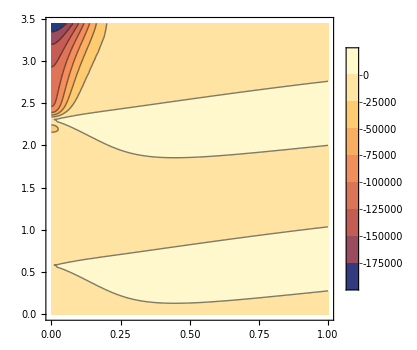
{-Graphics-,-Graphics3D-}

```mathematica
{ContourPlot[RDval[t,r],{r,0,1},{t,0,Delta},PlotRange->All,ImageSize->350,PlotLegends->Automatic],Plot3D[RDval[t,r],{r,0,1},{t,0,Delta},PlotRange->All,ImageSize->350,PlotLabel->"RD"]}
```

```mathematica
Clear[m]
```

```mathematica
m[t_,r_]=r/2(1-ia2[t,r])/.{f->finterp,ia2->ia2interp,Uu->Uinterp,Vv->Vinterp};
```

```mathematica
m[t,r]
```

1/2 r (1-InterpolatingFunction[{{0., 3.44545}, {0., 1.}}, <>][t,r])

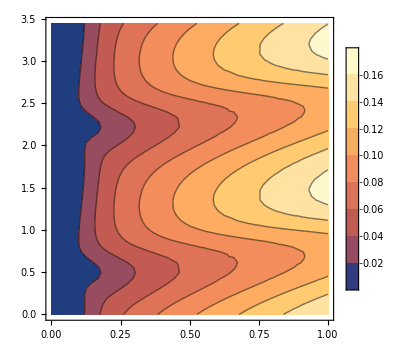
{-Graphics-,-Graphics3D-}

```mathematica
massplot={ContourPlot[m[t,r],{r,0,1},{t,0,Delta},PlotRange->All,ImageSize->350,PlotLegends->Automatic],Plot3D[m[t,r],{r,0,1},{t,0,Delta},PlotRange->All,ImageSize->350,PlotLabel->"m[t,r] = r/2(1-ia2[t,r])"]}
```

```mathematica
Export["massplot.pdf",massplot]
```

massplot.pdf

## Null coordinates and NEC angle

```mathematica
(*Define an additional grid for this calculation*)
nx=300;
nt=300;
xgrid=Range[0,0.1,0.1/nx];
tgrid=Range[0,Delta,Delta/nt];
```

```mathematica
ugrid=Range[-1,1,2/100];
```

```mathematica
vgrid=ugrid;
```

### Zero loci of U and V

```mathematica
(*Find zeros of interpolating functions*)
gamutx=ParallelTable[{xgrid[[i]],t/.FindRoot[Uinterp[t,xgrid[[i]]],{t,0.5}]},{i,2,nx+1}];
```

```mathematica
gamvtx=ParallelTable[{xgrid[[i]],t/.FindRoot[Vinterp[t,xgrid[[i]]],{t,0.5}]},{i,2,nx+1}];
```

```mathematica
(*Append value at x=0*)
ULcoeff=Import["L_taylor/uleft.junk"];
```

```mathematica
U1=dealias[ULcoeff[[;;,1]],Nt];
```

```mathematica
U1int=Interpolation[Transpose[{Range[0,Delta,Delta/Nt][[;;-2]],U1}]]
```

InterpolatingFunction[…]

```mathematica
(*Intersection point on t-axis*)
t0=t/.FindRoot[U1int[t],{t,0.5}]
```

0.577004

```mathematica
gamutx=Join[{{0,t0}},gamutx];
gamvtx=Join[{{0,t0}},gamvtx];
```

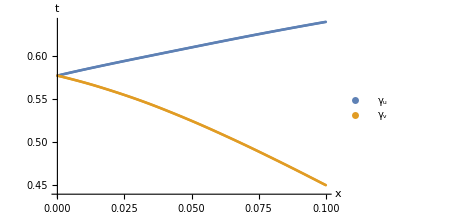

```mathematica
ListPlot[{gamutx,gamvtx},ImageSize->350,AxesLabel->{"x","t"},PlotLegends->{"γ_u","γ_v"}]
```

#### Find polynomial expression around NEC vertex; for plot

```mathematica
(*Rescale t to proper time at x=0*)
```

```mathematica
f0=dealias[Import["L_taylor/fleft.junk"][[;;,1]],Nt];
```

```mathematica
f00=Interpolation[Transpose[{Range[0,Delta,Delta/Nt][[;;-2]],f0}]][t0]
```

0.441045

```mathematica
gamuresc=gamutx;
gamvresc=gamvtx;
```

```mathematica
gamuresc[[;;,2]]=gamuresc[[;;,2]]*f00;
gamvresc[[;;,2]]=gamvresc[[;;,2]]*f00;
```

```mathematica
ord=4;
```

```mathematica
fitu=FindFit[gamuresc,Sum[Subscript[a, i]*x^i,{i,0,ord}],Table[Subscript[a, i],{i,0,ord}],x]
fitv=FindFit[gamvresc,Sum[Subscript[a, i]*x^i,{i,0,ord}],Table[Subscript[a, i],{i,0,ord}],x]
```

{a_0→0.25452,a_1→0.318072,a_2→-1.02685,a_3→12.1689,a_4→-61.8551}

{a_0→0.254458,a_1→-0.318686,a_2→-3.31016,a_3→7.56263,a_4→12.31}

```mathematica
gamupoly[x_]:=Sum[Subscript[a, i]*x^i,{i,0,ord}]/.fitu
```

```mathematica
gamvpoly[x_]:=Sum[Subscript[a, i]*x^i,{i,0,ord}]/.fitv
```

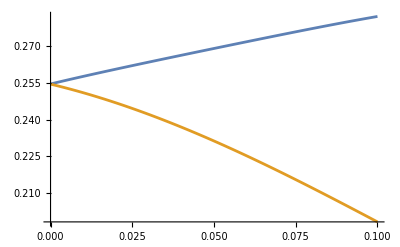

```mathematica
Plot[{gamupoly[x],gamvpoly[x]},{x,0,0.1}]
```

### Integrate PDEs for null coordinates (u,v)

```mathematica
vBC={v[Delta,x]==x,v[t,0]==(t-Delta)/Delta};
```

```mathematica
vnull=NDSolveValue[Join[{D[v[t,x],t]==-(x-finterp[t,x])*D[v[t,x],x]},vBC],v,{t,0,Delta},{x,0,1},Method->{"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->800}}}]
```

InterpolatingFunction[…]

```mathematica
uBC={u[Delta,x]==1-x,u[t,1]==(t-Delta)/Delta};
```

```mathematica
unull=NDSolveValue[Join[{D[u[t,x],t]==-(x+finterp[t,x])*D[u[t,x],x]},uBC],u,{t,0,Delta},{x,0,1},Method->{"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->800}}}]
```

InterpolatingFunction[…]

```mathematica
Plot3D[{unull[t,x],vnull[t,x]},{t,tgrid[[1]],tgrid[[-1]]},{x,0,1},AxesLabel->{"t","x"},PlotLegends->{"u","v"}]
```

-Graphics3D-

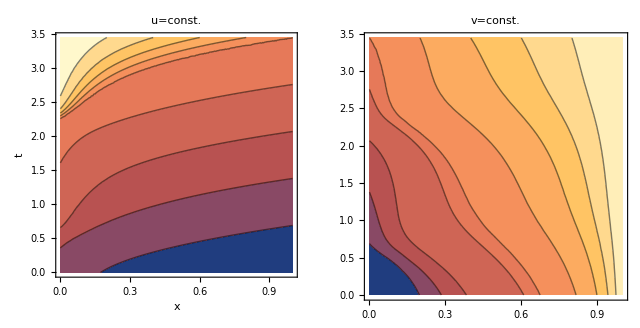

```mathematica
GraphicsRow[{ContourPlot[unull[t,x],{x,0,1},{t,tgrid[[1]],tgrid[[-1]]},AxesLabel->{"x","t"},PlotLabel->"u=const."],ContourPlot[vnull[t,x],{x,0,1},{t,tgrid[[1]],tgrid[[-1]]},PlotLabel->"v=const."]}]
```

```mathematica
Export["uvplot.pdf",%]
```

uvplot.pdf

```mathematica
NSolve[{u==unull[t[u,v],x[u,v]],v==vnull[t[u,v],x[u,v]]},{t,x},Reals]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[{u==InterpolatingFunction[…][t[u,v],x[u,v]],v==InterpolatingFunction[…][t[u,v],x[u,v]]},{t,x},ℝ]

```mathematica
txofuv[u_,v_]:=Module[{t,x},
{t,x}/.FindRoot[{0.2==unull[t,x],0==vnull[t,x]},{{t,0},{x,0}}]//Quiet];
```

```mathematica
txofuv[0.2,0]
```

{2.5061,0.0749398}

```mathematica
unull[t,x]/.{t->2.50609661235447,x->0.07493979389035642}
```

0.2

### Inverse trafo

```mathematica
tofuv=Flatten[Table[{unull[tgrid[[i]],xgrid[[j]]],vnull[tgrid[[i]],xgrid[[j]]],tgrid[[i]]},{i,1,nt},{j,1,nx}],1]
```

```mathematica
xofuv=Flatten[Table[{unull[tgrid[[i]],xgrid[[j]]],vnull[tgrid[[i]],xgrid[[j]]],xgrid[[j]]},{i,1,nt},{j,1,nx}],1]
```

```mathematica
tofuvint=Interpolation[tofuv];
xofuvint=Interpolation[xofuv];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
tofuvint[""]
```

```mathematica
Plot3D[xofuvint[u,v],{u,-1,1},{v,-1,1}]
```

-Graphics3D-

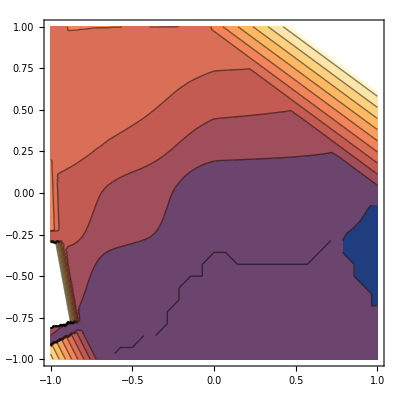

```mathematica
ContourPlot[xofuvint[u,v],{u,-1,1},{v,-1,1}]
```

```mathematica
uvdomain=xofuv;
```

```mathematica
uvdomain[[;;,3]]=ConstantArray[1,nx*nt];
```

```mathematica
a=Interpolation[uvdomain]
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

InterpolatingFunction[…]

```mathematica
Plot3D[a[u,v],{u,-1,1},{v,-1,1}]
```

-Graphics3D-

```mathematica
ListPlot3D[uvdomain]
```

-Graphics3D-

### coordinate transformation

```mathematica
tbaroftx=Flatten[Table[{Vinterp[tgrid[[i]],xgrid[[j]]],tgrid[[i]],xgrid[[j]]},{i,1,nt},{j,1,nx}],1];
```

```mathematica
gamutx[[10]]//N
```

{0.018,0.589477}

```mathematica
temp=Vinterp[gamutx[[20,1]],gamutx[[20,2]]]
```

0.0885579

```mathematica
Uinterp[temp,0*temp]
```

0.

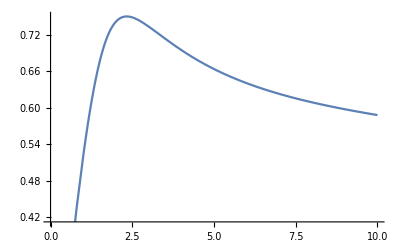

```mathematica
Plot[Uinterp[temp,x*temp],{x,0,10}]
```

```mathematica
FindRoot[Uinterp[temp,x*temp]==0,{x,5}]
```

InterpolatingFunction::dmval: Input value {0.102422,3.26724} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.102422,6.03821} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.102422,1.31268} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→10.385}

```mathematica
Uinterp[gamvtx]
```

```mathematica
gamuuv=Table[{unull[gamutx[[i,2]],gamutx[[i,1]]],vnull[gamutx[[i,2]],gamutx[[i,1]]]},{i,1,nx+1}];
gamvuv=Table[{unull[gamvtx[[i,2]],gamvtx[[i,1]]],vnull[gamvtx[[i,2]],gamvtx[[i,1]]]},{i,1,nx+1}];
```

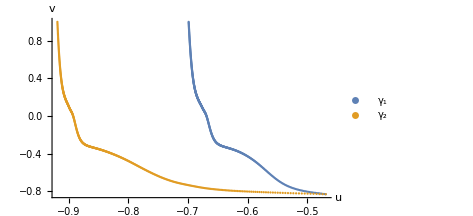

```mathematica
ListPlot[{gamuuv,gamvuv},ImageSize->350,AxesLabel->{"u","v"},PlotLegends->{"γ_1","γ_2"}]
```

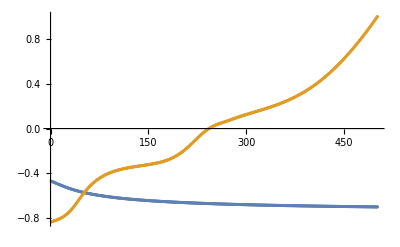

```mathematica
ListPlot[{gamuuv[[;;,1]],gamuuv[[;;,2]]}]
```

```mathematica
c=gamuuv[[;;,1]]/gamvuv[[;;,1]];
```

```mathematica
u0=gamuuv[[1,1]]
v0=gamvuv[[1,2]]
```

-0.469068

-0.832532

```mathematica
gam1testtx=Interpolation[gamutx];
gam2testtx=Interpolation[gamvtx];
gam1testuv=Interpolation[gamuuv]
gam2testuv=Interpolation[gamvuv]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
unull[gam1testtx[0],0]
vnull[gam1testtx[0],0]
```

-0.469068

-0.832532

```mathematica
unull[gam2testtx[0],0]
vnull[gam2testtx[0],0]
```

-0.469068

-0.832532

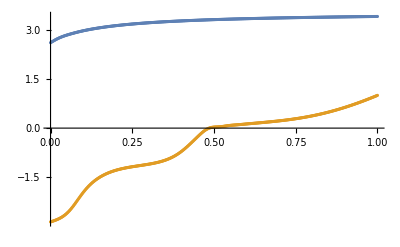

```mathematica
ListPlot[{Transpose[{Range[0,1,1/(nx-1)],gam1uv[[;;,1]]}],Transpose[{Range[0,1,1/(nx-1)],gam1uv[[;;,2]]}]}]
```

```mathematica
gam1uv[[1]]
```

{2.60711,-2.86278}

```mathematica
uofubar[[1]]
```

{0,2.60711}

```mathematica
ubarofu=Interpolation[Transpose[{gam1uv[[;;,1]],Range[0,1,1/(nx-1)]}]]
vbarofv=Interpolation[Transpose[{gam1uv[[;;,2]],Range[0,1,1/(nx-1)]}]]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
uofubar=Interpolation[Transpose[{Range[0,1,1/(nx-1)],gam1uv[[;;,1]]}]];
vofvbar=Interpolation[Transpose[{Range[0,1,1/(nx-1)],gam1uv[[;;,2]]}]];
```

```mathematica
gam1uvbar=Transpose[{Range[0,1,1/(nx-1)],Range[0,1,1/(nx-1)]}];
```

```mathematica
gam1uvbar=Table[{ubarofu[gam1uv[[i,1]]],vbarofv[gam1uv[[i,2]]]},{i,1,nx}];
gam2uvbar=Table[{ubarofu[gam2uv[[i,1]]],vbarofv[gam2uv[[i,2]]]},{i,100,nx}];
```

InterpolatingFunction::dmval: Input value {-0.741178} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.742725} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.744261} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

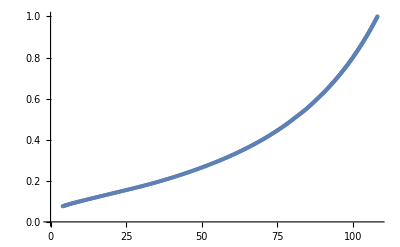

```mathematica
ListPlot[gam2uvbar]
```

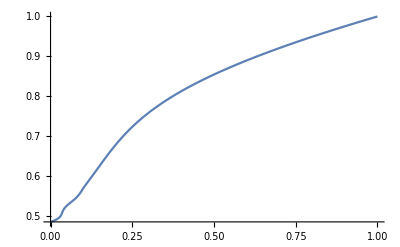

```mathematica
Plot[vofvbar[vbar],{vbar,0,1}]
```